```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy485-optics"]

fs=Style[#,FontSize->14]&;
```

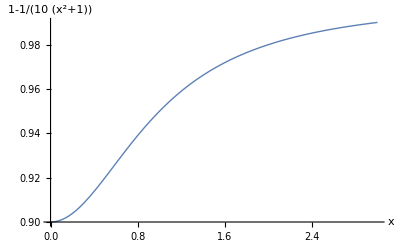

```mathematica
k[x_, a_] := 1 - a/(1 + x^2)

modernOpticsLecture20Fig5 = Module[ {a},
a  = 1/10 ;
Plot[
k[x, a], {x, 0, 3}
, PlotRange -> Full
, PlotStyle->Thick
, AxesLabel -> {x // fs, (1-a/(x^2+1)) // fs}
]]
```

```mathematica
peeters`exportForLatex["modernOpticsLecture20Fig5",modernOpticsLecture20Fig5]
```

{modernOpticsLecture20Fig5.eps,modernOpticsLecture20Fig5pn.png}